```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/Dhybrid/math"];
```

```mathematica
Data=Import["data10-2.csv"];
```

```mathematica
NcvsPz=Map[{#[[4]],#[[5]]}&,Data];
```

```mathematica
χ2[Π_]=Log[(2/π)^(1/4)Sqrt[Π/(2 10^-9)]];
Nc[Π_]=(Sqrt[χ2[Π]]/2+1/(4Sqrt[χ2[Π]]))Π;
calPc[Π_]=Π/(2Sqrt[2π]χ2[Π]);
```

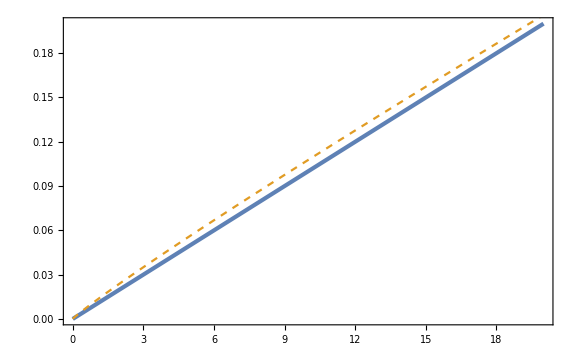

```mathematica
Show[Plot[0.01x,{x,0,20}],ParametricPlot[{Nc[Π],calPc[Π]},{Π,0,20},PlotStyle->{Color[2],Dashed}]]
```

```mathematica
Show[ListPlot[NcvsPz,Joined->False,FrameLabel->{Subscript[𝒩, "c"],Subscript[𝒫, ζ][Subscript[k, "c"]]}],Plot[0.01x,{x,0,30},PlotStyle->{Black,Dashed,AbsoluteThickness[2]}]]
```

-Graphics-

```mathematica
Show[ListPlot[NcvsPz,Joined->False],ParametricPlot[{Nc[Π],calPc[Π]},{Π,0,20},PlotStyle->{Color[2],AbsoluteThickness[3]}]]
```

-Graphics-

```mathematica
NoCubic=Select[Data,#[[3]]>1&];
NcvsPzNoCubic=Map[{#[[4]],#[[5]]}&,NoCubic];
```

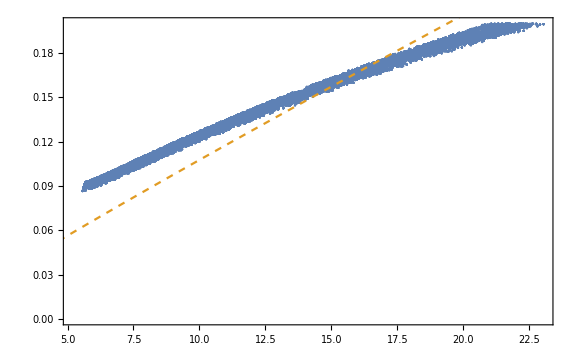

```mathematica
Show[ListPlot[NcvsPzNoCubic,Joined->False],ParametricPlot[{Nc[Π],calPc[Π]},{Π,0,20},PlotStyle->{Color[2],Dashed}]]
```

```mathematica
Clear["Global`*"]
ResourceFunction["MaTeXInstall"][]

mag=1.6;
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color,fourier}"}];
texStyle={FontFamily->(*"Latin Modern Roman"*)"Fourier",FontSize->17};
```

PacletObject[…]

```mathematica
SetDirectory[NotebookDirectory[]];
dataall=Import["data10-2.csv","CSV"];


(*  dataform: 
{Pi^2,mu2/Mpl,mu3/Mpl,Nc,Pzeta,ns50,ns54,running50,running54,4,ntot,xifend,chifend,(V0-Vend)/V0 }  
*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

{c0→4.82619,c12→1.3325}{c0→-86.971,c1→0.,c2→0.,c12→44.1363}{c0→8.32751,cm2→0.358988,cth→0.}{cmm1→5.47968,cmm2→0.00600205}

{c0→3.69461,c12→1.23754}{c0→-60.0702,c1→0.,c2→0.,c12→35.9092}{c0→-4.26768,cm2→0.306403,cth→0.}{cmm1→4.25035,cmm2→0.00466098}

{c0→2.24252,c12→1.14836}{c0→-51.4548,c1→0.,c2→0.,c12→33.4163}{c0→-23.2415,cm2→0.297035,cth→0.}{cmm1→3.63716,cmm2→0.00349275}

FindFit::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{c0→1.23617,c12→1.09574}{c0→-48.3235,c1→0.,c2→0.,c12→32.4266}{c0→-37.3665,cm2→0.29473,cth→0.}{cmm1→3.24847,cmm2→0.00300873}

FindFit::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{c0→0.725033,c12→1.04653}{c0→-48.3251,c1→0.,c2→0.,c12→32.5581}{c0→-40.3049,cm2→0.265081,cth→0.}{cmm1→3.18293,cmm2→0.00263753}

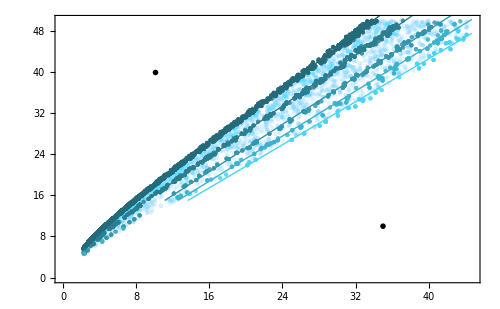

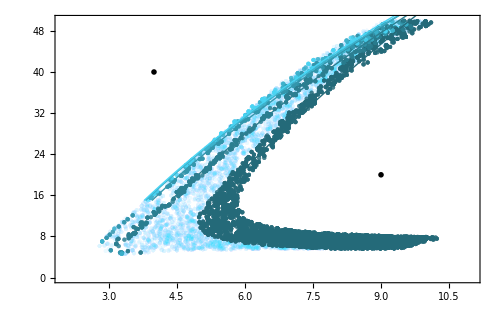

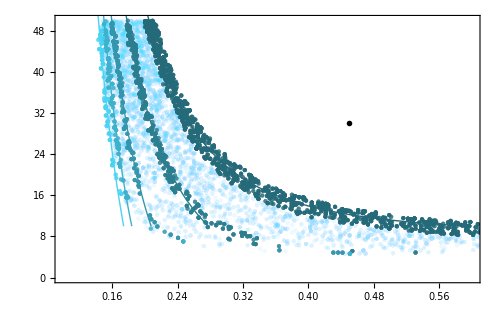

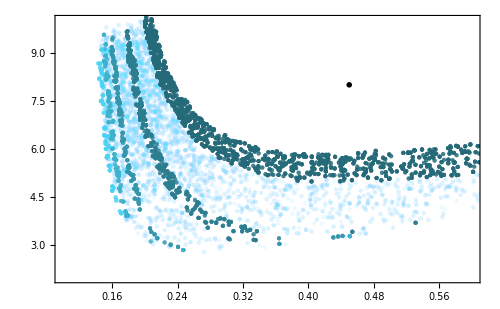

```mathematica
plnum=5;
pl1=Table[{},{k,1,plnum}];
pl12=Table[{},{k,1,plnum}];
pl2=Table[{},{k,1,plnum}];
pl3=Table[{},{k,1,plnum}];
pl23=Table[{},{k,1,plnum}];

plfit1=Table[{},{k,1,plnum}];
plfit12=Table[{},{k,1,plnum}];
plfit2=Table[{},{k,1,plnum}];
plfit22=Table[{},{k,1,plnum}];
plfit3=Table[{},{k,1,plnum}];
plfit23=Table[{},{k,1,plnum}];

dataplall12={};
dataplall2={};
dataplall3={};
dataplall23={};

For[k=1,k<plnum+1,k++,
data1={};
data1fit={};
data12={};
data12fit={};
data2={};
data2fit1={};
data2fit2={};
data3={};
data3fit={};
datarunning={};
data23={};
data23fit={};

nsdiv=0.0042;
ns=0.9649;

Pz1=0.1;
If[k==1,Pz2=0.05];
If[k==2,Pz1=Pz2;Pz2=0.02];
If[k==3,Pz1=Pz2;Pz2=0.01];
If[k==4,Pz1=Pz2;Pz2=0.005];
If[k==5,Pz1=Pz2;Pz2=0.001];

frac= 1.1;
If[k==1,Pz=0.1];
If[k==2,Pz=0.05];
If[k==3,Pz=0.02];
If[k==4,Pz=0.01];
If[k==5,Pz=0.005];

For[i=1,i≤ Length[dataall],i++,
If[dataall[[i,7]]<ns+nsdiv &&dataall[[i,7]]>ns-nsdiv
,

(*If[dataall[[i,5]]<Pz1 &&dataall[[i,5]]>Pz2
,
data1=Append[data1,{dataall[[i,1]] ,dataall[[i,4]]}];
data12=Append[data12,{Sqrt[dataall[[i,1]]] ,dataall[[i,4]]}]; (* Pi vs Nc *)
data2=Append[data2,{dataall[[i,2]] ,dataall[[i,4]]}]; (* mu_2 vs Nc *)
data3=Append[data3,{dataall[[i,3]] ,dataall[[i,4]]}];  (* mu_3 vs Nc *)
];*)
If[k==1,
If[dataall[[i,5]]<0.1 &&dataall[[i,5]]>0.005,
dataplall12=Append[dataplall12,{Sqrt[dataall[[i,1]]] ,dataall[[i,4]]}];
dataplall2=Append[dataplall2,{dataall[[i,2]] ,dataall[[i,4]]}];
dataplall3=Append[dataplall3,{dataall[[i,3]] ,dataall[[i,4]]}];
dataplall23=Append[dataplall23,{dataall[[i,3]] ,dataall[[i,2]]}];
];
];

If[dataall[[i,5]]<Pz frac &&dataall[[i,5]]>Pz/ frac
,

data1=Append[data1,{dataall[[i,1]] ,dataall[[i,4]]}];
data12=Append[data12,{Sqrt[dataall[[i,1]]] ,dataall[[i,4]]}]; (* Pi vs Nc *)
data2=Append[data2,{dataall[[i,2]] ,dataall[[i,4]]}]; (* mu_2 vs Nc *)
data3=Append[data3,{dataall[[i,3]] ,dataall[[i,4]]}];  (* mu_3 vs Nc *)
data23=Append[data23,{dataall[[i,3]] ,dataall[[i,2]]}];  (* mu_3 vs mu_2 *)

If[dataall[[i,4]]>10,
data3fit=Append[data3fit,{dataall[[i,3]] ,dataall[[i,4]]}];

];

If[dataall[[i,4]]>15,
data1fit=Append[data1fit,{dataall[[i,1]] ,dataall[[i,4]]}];
data12fit=Append[data12fit,{Sqrt[dataall[[i,1]]] ,dataall[[i,4]]}];
data2fit1=Append[data2fit1,{dataall[[i,2]] ,dataall[[i,4]]}];
data23fit=Append[data23fit,{dataall[[i,3]] ,dataall[[i,2]]}];
];

]
]
];
style={Hue[0.53,(*0.1 2^k*)0.7,0.4 2^(k/4)],Thick};
stylep={Hue[0.53,(*0.1 2^k,0.5+0.08k*)0.7,0.4 2^(k/4)],Opacity[0.3],PointSize[Small]};
stylepall={Hue[0.53,(*0.1 2^k,0.5+0.08k*)0.7,1],Opacity[0.02],PointSize[Small]};

(* *******reduce the number of data ******* *)
reducenum=1;

fitfunc12[x_]:= c0+c12 x;
f12=FindFit[data12fit,fitfunc12[x],{c0,c12},x];
plfit12[[k]]=Plot[fitfunc12[x] /. f12,{x,0,Sqrt[2000]},PlotRange-> {15,60}, PlotStyle->style];
data12=Table[data12[[i]],{i,1,Length[data12],reducenum}];
pl12[[k]]=ListPlot[data12,PlotStyle->(* Opacity[1/k]*)stylep,PlotRange-> {{0,Sqrt[2000]},{0,50}},

Frame->True,FrameStyle->BlackFrame,
Axes-> None,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->mag
,BaseStyle->texStyle
,FrameLabel->  {
MaTeX["\\Pi",Magnification->mag],MaTeX["\\mathcal{N}_{\\rm c}",Magnification->mag]
(*Style["(r-r_+)/M_BH",Italic,FontSize->23],Style["ϕ(r)/μ",Italic,FontSize->23]*)}
,LabelStyle->texStyle(*{Black,FontFamily->"Georgia",FontSize->18}*)
,ImageSize->(*300*)500,AspectRatio->2/(1+Sqrt[5])
,Epilog->{
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\lesssim 0.005",Magnification-> mag(*,Magnification->1.4*)],{35,10},Automatic,Automatic,{1,-0.}]
,
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\gtrsim 0.1",Magnification-> mag(*,Magnification->1.4*)],{10,40},Automatic,Automatic,{1,-0.}]
}
];

dataplall12=Table[dataplall12[[i]],{i,1,Length[dataplall12],reducenum}];
pl12all=ListPlot[dataplall12,PlotStyle->(* Opacity[1/k]*)stylepall,
PlotRange-> {{0,Sqrt[2000]},{0,50}},

Frame->True,FrameStyle->BlackFrame,
Axes-> None,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->mag
,BaseStyle->texStyle
,FrameLabel->  {
MaTeX["\\Pi",Magnification->mag],MaTeX["\\mathcal{N}_{\\rm c}",Magnification->mag]
(*Style["(r-r_+)/M_BH",Italic,FontSize->23],Style["ϕ(r)/μ",Italic,FontSize->23]*)}
,LabelStyle->texStyle(*{Black,FontFamily->"Georgia",FontSize->18}*)
,ImageSize->(*300*)500,AspectRatio->2/(1+Sqrt[5])
,Epilog->{
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\lesssim 0.005",Magnification-> mag(*,Magnification->1.4*)],{35,10},Automatic,Automatic,{1,-0.}]
,
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\gtrsim 0.1",Magnification-> mag(*,Magnification->1.4*)],{10,40},Automatic,Automatic,{1,-0.}]
}
];


fitfunc2[x_]:=c0+ 0 c1 x+  c12 Sqrt[x]+0  c2 x^2;
f2=FindFit[data2fit1,fitfunc2[x],{c0,c1,c2, c12},x];
plfit2[[k]]=Plot[fitfunc2[x] /. f2,{x,0,12},PlotRange-> {15,60},PlotStyle->style];
data2=Table[data2[[i]],{i,1,Length[data2],reducenum}];
pl2[[k]]=ListPlot[data2,PlotStyle->(* Opacity[1/k]*)stylep,PlotRange-> {{2,11},{0,50}}
,Frame->True,FrameStyle->BlackFrame
,Axes-> None
,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->mag
,BaseStyle->texStyle
,FrameLabel->  {
MaTeX["\\mu_2/M_{\\rm pl}",Magnification->mag],MaTeX["\\mathcal{N}_{\\rm c}",Magnification->mag]
(*Style["(r-r_+)/M_BH",Italic,FontSize->23],Style["ϕ(r)/μ",Italic,FontSize->23]*)}
,LabelStyle->texStyle(*{Black,FontFamily->"Georgia",FontSize->18}*)
,ImageSize->(*300*)500,AspectRatio->2/(1+Sqrt[5])
,Epilog->{
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\lesssim 0.005",Magnification-> mag(*,Magnification->1.4*)],{4,40},Automatic,Automatic,{1,-0.}]
,
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\gtrsim 0.1",Magnification-> mag(*,Magnification->1.4*)],{9,20},Automatic,Automatic,{1,-0.}]
}
];

dataplall2=Table[dataplall2[[i]],{i,1,Length[dataplall2],reducenum}];
pl2all=ListPlot[dataplall2,PlotStyle->(* Opacity[1/k]*)stylepall,
PlotRange-> {{2,11},{0,50}}
,Frame->True,FrameStyle->BlackFrame
,Axes-> None
,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->mag
,BaseStyle->texStyle
,FrameLabel->  {
MaTeX["\\mu_2/M_{\\rm pl}",Magnification->mag],MaTeX["\\mathcal{N}_{\\rm c}",Magnification->mag]
(*Style["(r-r_+)/M_BH",Italic,FontSize->23],Style["ϕ(r)/μ",Italic,FontSize->23]*)}
,LabelStyle->texStyle(*{Black,FontFamily->"Georgia",FontSize->18}*)
,ImageSize->(*300*)500,AspectRatio->2/(1+Sqrt[5])
,Epilog->{
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\lesssim 0.005",Magnification-> mag(*,Magnification->1.4*)],{4,40},Automatic,Automatic,{1,-0.}]
,
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\gtrsim 0.1",Magnification-> mag(*,Magnification->1.4*)],{9,20},Automatic,Automatic,{1,-0.}]
}
];
(*pl2[[k]]=Show[pl22,plfit2,plfit22];*)

fitfunc3[x_]:=c0(*+0 c1 x+ 0 c12 Sqrt[x]*)(*+0  c2 x^2+ 0 cm1 /x*)+  cm2/x^3;
f3=FindFit[data3fit,fitfunc3[x],{c0,cm2,cth},x];
plfit3[[k]]=Plot[fitfunc3[x] /. f3,{x,0.1,10},PlotRange -> {10,60},PlotStyle->style];
data3=Table[data3[[i]],{i,1,Length[data3],reducenum}];
pl3[[k]]=ListPlot[data3,PlotStyle->(* Opacity[1/k]*)stylep,PlotRange-> {{0.1,0.6},{0,50}}
,Frame->True,FrameStyle->BlackFrame
,Axes-> None
,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->mag
,BaseStyle->texStyle
,FrameLabel->  {
MaTeX["\\mu_3/M_{\\rm pl}",Magnification->mag],MaTeX["\\mathcal{N}_{\\rm c}",Magnification->mag]
(*Style["(r-r_+)/M_BH",Italic,FontSize->23],Style["ϕ(r)/μ",Italic,FontSize->23]*)}
,LabelStyle->texStyle(*{Black,FontFamily->"Georgia",FontSize->18}*)
,ImageSize->(*300*)500,AspectRatio->2/(1+Sqrt[5])
,Epilog->{
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\gtrsim 0.1",Magnification-> mag(*,Magnification->1.4*)],{0.45,30},Automatic,Automatic,{1,-0.}]
}
];


dataplall3=Table[dataplall3[[i]],{i,1,Length[dataplall3],reducenum}];
pl3all=ListPlot[dataplall3,PlotStyle->(* Opacity[1/k]*)stylepall

,PlotRange-> {{0.1,0.6},{0,50}}
,Frame->True,FrameStyle->BlackFrame
,Axes-> None
,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->mag
,BaseStyle->texStyle
,FrameLabel->  {
MaTeX["\\mu_3/M_{\\rm pl}",Magnification->mag],MaTeX["\\mathcal{N}_{\\rm c}",Magnification->mag]
(*Style["(r-r_+)/M_BH",Italic,FontSize->23],Style["ϕ(r)/μ",Italic,FontSize->23]*)}
,LabelStyle->texStyle(*{Black,FontFamily->"Georgia",FontSize->18}*)
,ImageSize->(*300*)500,AspectRatio->2/(1+Sqrt[5])
,Epilog->{
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\gtrsim 0.1",Magnification-> mag(*,Magnification->1.4*)],{0.45,30},Automatic,Automatic,{1,-0.}]
}
];


fitfunc23[x_]:=(*c0+ *)cmm1 Abs[(1- cmm2 x^(-3))]^(-1/2);
f23=FindFit[data23fit,{fitfunc23[x],{cmm1<10,cmm2<0.01}},{cmm1,cmm2},x];
plfit23[[k]]=Plot[fitfunc23[x] /. f23,{x,0.1,10},PlotRange -> {2,11},PlotStyle->style];

data23=Table[data23[[i]],{i,1,Length[data23],reducenum}];
pl23[[k]]=ListPlot[data23,PlotStyle->(* Opacity[1/k]*)stylep,PlotRange-> {{0.1,0.6},{2,10}}
,Frame->True,FrameStyle->BlackFrame
,Axes-> None
,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->mag
,BaseStyle->texStyle
,FrameLabel->  {
MaTeX["\\mu_3/M_{\\rm pl}",Magnification->mag],MaTeX["\\mu_2/M_{\\rm pl}",Magnification->mag]
(*Style["(r-r_+)/M_BH",Italic,FontSize->23],Style["ϕ(r)/μ",Italic,FontSize->23]*)}
,LabelStyle->texStyle(*{Black,FontFamily->"Georgia",FontSize->18}*)
,ImageSize->(*300*)500,AspectRatio->2/(1+Sqrt[5])
,Epilog->{
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\gtrsim 0.1",Magnification-> mag(*,Magnification->1.4*)],{0.45,30},Automatic,Automatic,{1,-0.}]
}
];

dataplall23=Table[dataplall23[[i]],{i,1,Length[dataplall23],reducenum}];
pl23all=ListPlot[dataplall23,PlotStyle->(* Opacity[1/k]*)stylepall

,PlotRange-> {{0.1,0.6},{2,10}}
,Frame->True,FrameStyle->BlackFrame
,Axes-> None
,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->mag
,BaseStyle->texStyle
,FrameLabel->  {
MaTeX["\\mu_3/M_{\\rm pl}",Magnification->mag],MaTeX["\\mu_2/M_{\\rm pl}",Magnification->mag]
(*Style["(r-r_+)/M_BH",Italic,FontSize->23],Style["ϕ(r)/μ",Italic,FontSize->23]*)}
,LabelStyle->texStyle(*{Black,FontFamily->"Georgia",FontSize->18}*)
,ImageSize->(*300*)500,AspectRatio->2/(1+Sqrt[5])
,Epilog->{
Inset[MaTeX["\\mathcal{P}_\\zeta^{\\rm (peak)} \\gtrsim 0.1",Magnification-> mag(*,Magnification->1.4*)],{0.45,8},Automatic,Automatic,{1,-0.}]
}
];


Print[f12,f2,f3,f23];

];



(*Show[pl12,plfit12]
Show[pl2,plfit2]
Show[pl3,plfit3]*)

Show[pl12all,pl12,plfit12]
Export["fig_Pi.pdf",%];
Show[pl2all,pl2,plfit2]
Export["fig_mu2.pdf",%];
Show[pl3all,pl3,plfit3]
Export["fig_mu3.pdf",%];
Show[pl23all,pl23(*,plfit23*)]
Export["fig_mu2_mu3.pdf",%];
```

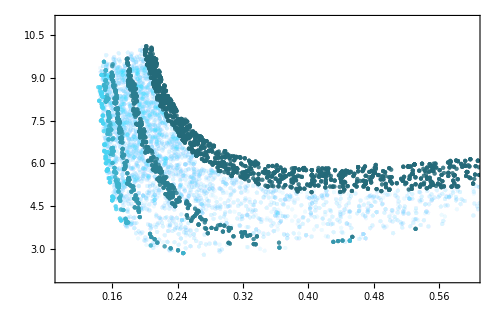

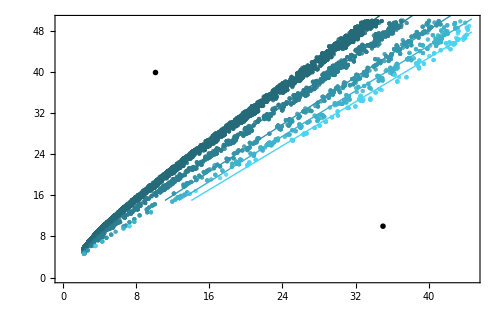

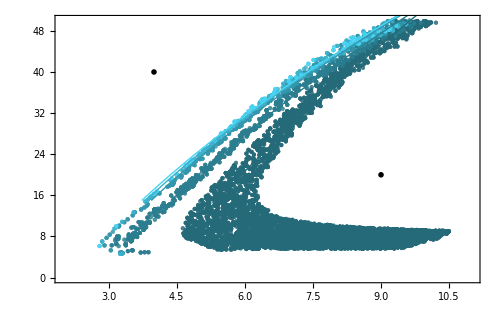

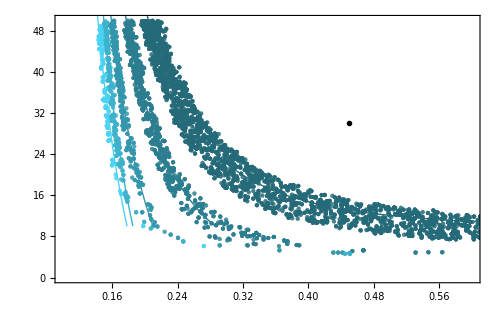

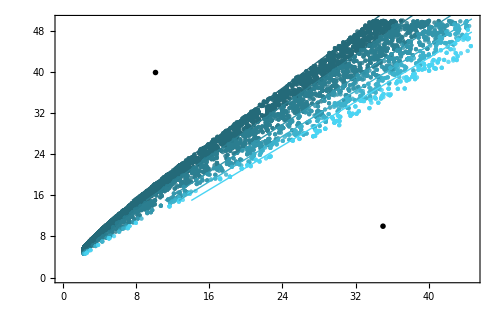

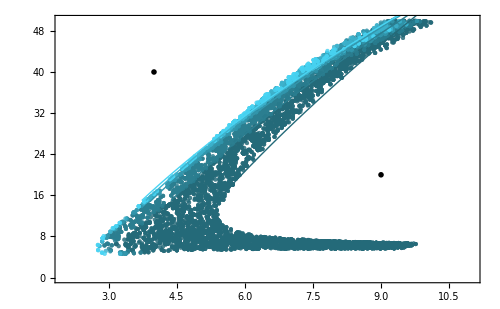

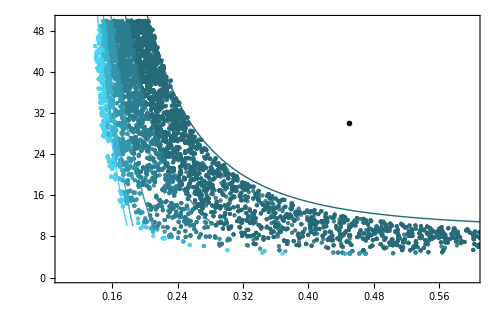

```mathematica
Show[pl23all,pl23]
```